R2 bigger resolution = (√2 | 0 | -√2 | -3 √2
0 | 5 | 0 | 0
1/(√2) | 0 | 1/(√2) | -9/(√2)
1/(√2) | 0 | 1/(√2) | -9/(√2))

GraficC2 = {{2 √2,3,-5 √2,-5 √2},{3 √2,3,-4 √2,-4 √2},{3 √2,5,-4 √2,-4 √2},{2 √2,5,-5 √2,-5 √2}}

GraficC3 = {{4 √2,15,-5 √2,-5 √2},{6 √2,15,-4 √2,-4 √2},{6 √2,25,-4 √2,-4 √2},{4 √2,25,-5 √2,-5 √2}}

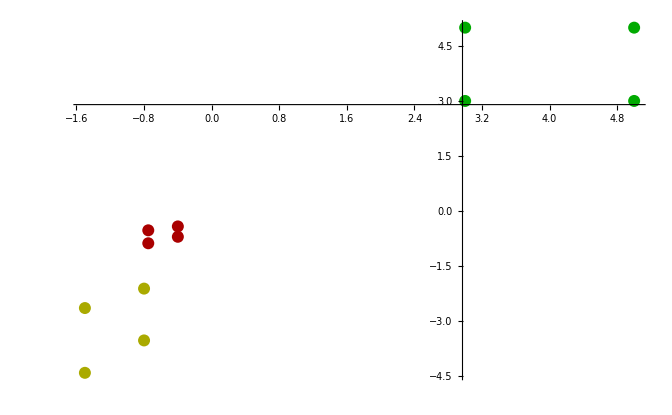

```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};




R=({{1/(√2), 0, -1/(√2), -3/(√2)}, {0, 1, 0, 0}, {1/(√2), 0, 1/(√2), -9/(√2)}, {1/(√2), 0, 1/(√2), -9/(√2)}});

(*R=({{√2, 0, -√2, -3 √2}, {0, 2, 0, 0}, {1/(√2), 0, 1/(√2), -9/(√2)}, {1/(√2), 0, 1/(√2), -9/(√2)}});*)

R2=({{√2, 0, -√2, -3 √2}, {0, 5, 0, 0}, {1/(√2), 0, 1/(√2), -9/(√2)}, {1/(√2), 0, 1/(√2), -9/(√2)}});

(*R=({{0.3782363431702456, -0.02963422169458394, -0.9252346089558885, 0.8122766811321841}, {0.0547643798389093, -0.9970205992520795, 0.05432115028130604, -0.03891454402441562}, {-0.9240877292801047, -0.07121613280416697, -0.37548652575340075, -0.5819727240620955}});

(*beide seiten gleich vergrößert einmal mit A = 2 und einmal mit A = 5*)
R2=({{0.3782363431702456, -0.02963422169458394, -0.9252346089558885, 0.8122766811321841}, {0.0547643798389093, -0.9970205992520795, 0.05432115028130604, -0.03891454402441562}, {-0.9240877292801047, -0.07121613280416697, -0.37548652575340075, -0.5819727240620955}})

R2=({{0.37823634317025645, -0.029634221694579306, -0.9252346089558846, 0.812276681132185}, {0.05476437983890481, -0.99702059925208, 0.05432115028130029, -0.03891454402441529}, {-0.9240877292801003, -0.07121613280416172, -0.37548652575341246, -0.5819727240620943}})

(*Beide Seiten unterschiedlich vergrößert*)
(*2:5*)
R2=({{0.37537165569848785, -0.028932796551008146, -0.9264226969272253, 0.809493518916553}, {0.054167116232524064, -0.99711962662921, 0.053088357573733536, -0.038587552905375605}, {-0.9252902483098087, -0.07010951058567128, -0.3727232390235543, -0.585859405995048}});
(*5:8*)

R2=({{0.37772971403468225, -0.029454595550847007, -0.92544729181959, 0.8115578833169436}, {0.0545229461520091, -0.9970519469910799, 0.05398762213880197, -0.038850518383715095}, {-0.9243092077211947, -0.07085084193030489, -0.3750101954875159, -0.5829789355091987}});

R2=({{-1.7677669529663687, 0., 1.7677669529663687, 5.303300858899108}, {0., -6.4, 0., 0.}, {-0.7071067811865475, 0., -0.7071067811865475, 6.363961030678928}, {0.7071067811865475, 0., 0.7071067811865475, -6.363961030678928}});

R2=({{0.14142135623731217, 4.1112876077063177*^-16, -0.989949493661166, -0.31622776601683605}, {8.537458941746366*^-16, 0.9999999999999999, 6.024606892920157*^-16, 1.1102230246251565*^-15}, {-0.9899494936611659, 6.99393060951908*^-16, -0.1414213562373125, -0.9486832980505144}});

R={{R[[1,1]],R[[1,2]],R[[1,3]],R[[1,4]]},{R[[2,1]],R[[2,2]],R[[2,3]],R[[2,4]]},{R[[3,1]],R[[3,2]],R[[3,3]],R[[3,4]]},{0,0,0,1}};
R2={{R2[[1,1]],R2[[1,2]],R2[[1,3]],R2[[1,4]]},{R2[[2,1]],R2[[2,2]],R2[[2,3]],R2[[2,4]]},{R2[[3,1]],R2[[3,2]],R2[[3,3]],R2[[3,4]]},{0,0,0,1}};*)

(*R={{3/(5 √2)+(√2)/5,0,1/(5 √2)-(3 √2)/5,-1/3},{0,1,0,0},{-1/(5 √2)+(3 √2)/5,0,3/(5 √2)+(√2)/5,-1},{0,0,0,1}};


R2={{3/(5 √2)+(√2)/5,0,1/(5 √2)-(3 √2)/5,-3/(√2)},{0,1,0,0},{-1/(5 √2)+(3 √2)/5,0,3/(5 √2)+(√2)/5,-9/(√2)},{0,0,0,1}};*)



Print["R2 bigger resolution = ", MatrixForm[R2]];

GraficC1={};
GraficC2={};
GraficC3={};

AppendTo[GraficC1, a];
AppendTo[GraficC1, b];
AppendTo[GraficC1, c];
AppendTo[GraficC1, d];

aa=R.a;
bb=R.b;
cc=R.c;
dd=R.d;

aaa=R2.a;
bbb=R2.b;
ccc=R2.c;
ddd=R2.d;

AppendTo[GraficC2, aa];
AppendTo[GraficC2, bb];
AppendTo[GraficC2, cc];
AppendTo[GraficC2, dd];

AppendTo[GraficC3, aaa];
AppendTo[GraficC3, bbb];
AppendTo[GraficC3, ccc];
AppendTo[GraficC3, ddd];

(*Print["GraficC1 = ", GraficC1];*)
Print["GraficC2 = ", GraficC2];
Print["GraficC3 = ", GraficC3];

GraficC1= Map[{#[[1]],#[[2]],#[[3]]}&,GraficC1];
GraficC2= Map[{#[[1]],#[[2]],#[[3]]}&,GraficC2];
GraficC3= Map[{#[[1]],#[[2]],#[[3]]}&,GraficC3];

For[i=1, i≤ 4, i++,
GraficC2[[i]]=GraficC2[[i]]/GraficC2[[i,3]];
GraficC3[[i]]=GraficC3[[i]]/GraficC3[[i,3]]

];

(*Print["GraficC1 = ", GraficC1];
Print["GraficC2 = ", GraficC2];
Print["GraficC3 = ", GraficC3];*)

GraficC1= Map[{#[[1]],#[[2]]}&,GraficC1];
GraficC2= Map[{#[[1]],#[[2]]}&,GraficC2];
GraficC3= Map[{#[[1]],#[[2]]}&,GraficC3];

G1=Show[ListPlot[GraficC1[[1;;4]],PlotStyle->Darker[Green]]];
G2=Show[ListPlot[GraficC2[[1;;4]],PlotStyle->Darker[Red]]];
G3=Show[ListPlot[GraficC3[[1;;4]],PlotStyle->Darker[Yellow]]];
Print[Show[G1,G2,G3,PlotRange->All]]
```

```mathematica
N[-1/(5 √2)+(3 √2)/5]
```

0.707107